Okeefe Niemann
5/23/2014
1281465
PHYS 115

## Assignment 7

### Question 1 :

Part a :

```mathematica
sphericalbessel[l_, x_] := FunctionExpand[SphericalBesselJ[l,x]]
```

```mathematica
sphericalneumann[l_, x_] := FunctionExpand[SphericalBesselY[l,x]]
```

Part b :

```mathematica
sphericalbessel[0,x]
```

Sin[x]/x

```mathematica
sphericalbessel[1, x]
```

-Cos[x]/x+Sin[x]/x^2

```mathematica
sphericalbessel[10,x] // Simplify
```

-1/x^11(55 x (11904165-1670760 x^2+51597 x^4-468 x^6+x^8) Cos[x]+(-654729075+310134825 x^2-18918900 x^4+315315 x^6-1485 x^8+x^10) Sin[x])

Part c:

```mathematica
Normal[Series[sphericalbessel[10,x], {x, 0, 14}] ]
```

x^10/13749310575-x^12/632468286450+x^14/63246828645000

```mathematica
Normal[Series[sphericalneumann[10,x], {x, 0, -7}] ]
```

-654729075/x^11-34459425/(2 x^9)-2027025/(8 x^7)

Part d:

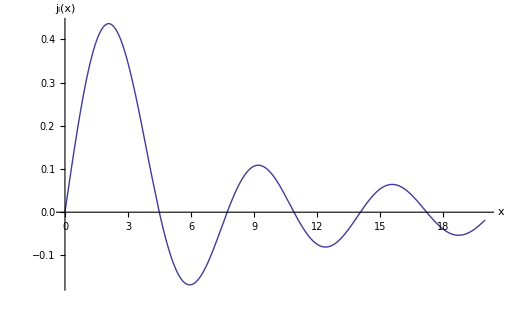

```mathematica
Plot[sphericalbessel[1,x], {x, 0, 20}, AxesLabel -> {x, Subscript[j, l][x]}]
```

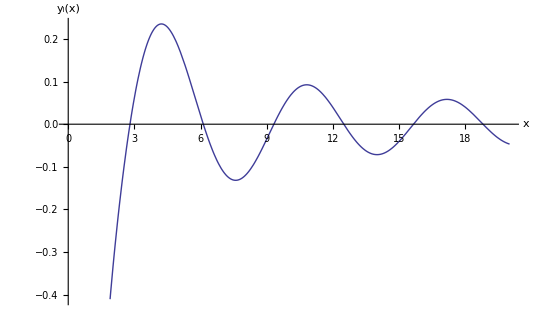

```mathematica
Plot[sphericalneumann[1,x], {x, 0, 20}, AxesLabel -> {x, Subscript[y, l][x]}]
```

### Question 2

Part a:

```mathematica
Normal[Series[Tanh[x], {x, 0, 20}]]
```

x-x^3/3+(2 x^5)/15-(17 x^7)/315+(62 x^9)/2835-(1382 x^11)/155925+(21844 x^13)/6081075-(929569 x^15)/638512875+(6404582 x^17)/10854718875-(443861162 x^19)/1856156927625

Part b :

```mathematica
Normal[InverseSeries[Series[Tanh[x], {x, 0, 20}]]]
```

x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15+x^17/17+x^19/19

### Question 3

```mathematica
Clear["Global`*"]
```

Part a :

```mathematica
integral := Integrate[x^4 Exp[x]/(Exp[x]-1)^2, {x, 0, Infinity}]
```

```mathematica
9 (T/Subscript[Θ, D])^3integral
```

(12 π^4 T^3)/(5 Θ_D^3)

Part b:
Comment - In the following parts, y = T / Θ_D.

```mathematica
integral1[y_] = Integrate[x^4 Exp[x]/(Exp[x]-1)^2, {x, 0, y}]
```

ConditionalExpression[-(4 π^4)/15+1/(-1+ⅇ^y)(-ⅇ^y y^4-4 y^3 Log[1-ⅇ^y]+4 ⅇ^y y^3 Log[1-ⅇ^y]+12 (-1+ⅇ^y) y^2 PolyLog[2,ⅇ^y]-24 (-1+ⅇ^y) y PolyLog[3,ⅇ^y]-24 PolyLog[4,ⅇ^y]+24 ⅇ^y PolyLog[4,ⅇ^y]),ⅇ^y≤1]

```mathematica
Limit[9 / y^3integral1[y], y -> 0, Direction -> 1]
```

3

Part c :

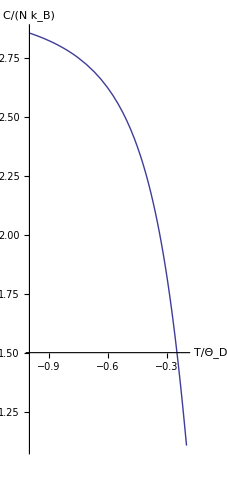

```mathematica
ParametricPlot[{1 / y, 9 / y^3 integral1[y]}, {y, -5, -1}, AxesLabel -> {T/Subscript[Θ, D], C / (N Subscript[k, B])}]
```

### Question 4

Part a:

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[Plot[{m =  Tanh[J m / T], m}, {m, -2, 2}, AxesLabel -> {"m", f["m"]}, PlotLegends -> {"m = TanhJm/T", "f(m)= m"}], {J, 0, 1}, {T, .1, 1}]
```

Part b:

```mathematica
Manipulate[Plot[{m =  Tanh[J m / T], m}, {m, -2, 2},AxesLabel -> {"m", f["m"]}, PlotLegends -> {"m = TanhJm/T", "f(m)= m"}], {J, 0, 1}, {T, .1, 1} ]
```

Comment: As shown above, the only solution is m=0 for T > J, while two extra symmetric solutions begin to appear when J > T.

Part c:

See back handwritten page

Part d:

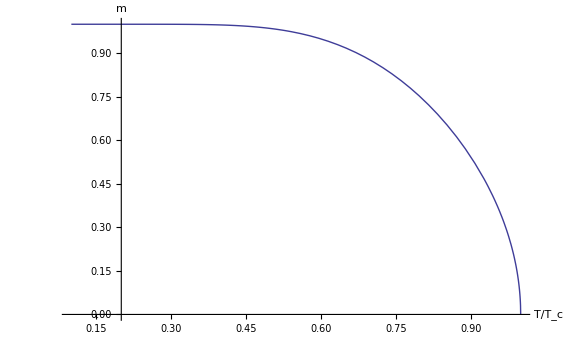

```mathematica
Plot[{Tanh[1 / t Sqrt[3 ( 1 - t)]]}, {t, 0.1, 1}, AxesLabel-> {"T" / Subscript["T", c], "m"}]
```

T/T_c cannot go all the way to zero or else the magnetization will go to infinity.

Part e:

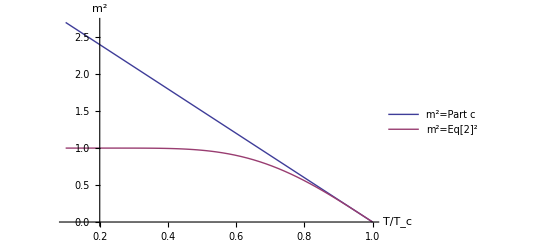

```mathematica
Plot[{3(1-t),  Tanh[1 / t Sqrt[3 ( 1 - t)]]^2}, {t, 0.1, 1}, AxesLabel-> {"T" / Subscript["T", c], "m"^2}, PlotLegends -> {"m^2=Part c", "m^2=Eq[2]^2"}]
```

As shown above, the equation for magnetization agrees with the approximation as T/T_c approaches one.

### Question 5

Part a :

```mathematica
Clear["Global`*"]
```

```mathematica
k=0.004;
g=9.81;
sol:=NDSolve[{x''[t]==-k x'[t] Sqrt[y'[t]^2+x'[t]^2],y''[t]==-k y'[t] Sqrt[y'[t]^2+x'[t]^2]-g,x[0]==0,y[0]==0,x'[0]==v Cos[theta],y'[0]==v Sin[theta]},{x,y},{t,0,1000}]
yy[t_] := y[t] /. sol[[1]]; 
xx[t_] := x[t] /. sol[[1]];
tfinal[theta_] := (sol; yy[t_]; xx[t_]; t /. FindRoot[yy[t], {t, 1, 1000}, MaxIterations -> 50])
xfinal[theta_?NumericQ] := xx[tfinal[theta]]
xmax[vv_] :=(v=vv; FindMaximum[xfinal[theta], {theta, 0, 2}][[1]])
```

The above block of code numerically solves the differential equations for a projectile and extracts the answers. It then calculates the value of theta for which the projectile travels the longest and passes this calculation along xx[t_], which in turn calculates the distance covered in that amount of time. I then created a function in which the initial velocity is variable for easy calculations as well as generality.

```mathematica
xmax[50]
```

150.21

```mathematica
xmaxnf[50]
```

254.842

As seen above, the maximum distance the projectile travels with the absence of friction is about 100m greater than if it were to be traveling with friction present.

Part b :

```mathematica
nofriction[theta_] := v^2 Sin[2 theta] / g
xmaxnf[vv_] :=(v=vv; FindMaximum[nofriction[theta], {theta, 0, 2}][[1]])
```

The above function is the distance the projectile travels in the x direction without friction for any initial veloctiy.

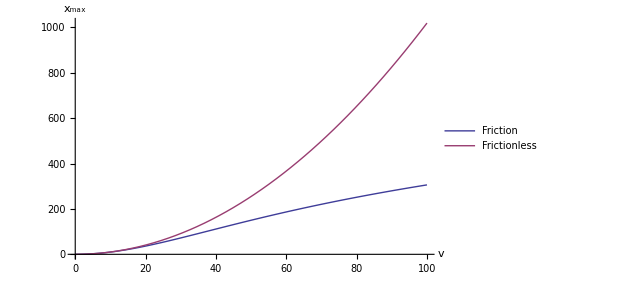

```mathematica
Plot[{xmax[v], xmaxnf[v]}, {v, 0, 100}, AxesLabel-> {"v", Subscript["x", "max"]}, PlotLegends-> {"Friction", "Frictionless"}]
```

The above graph shows that the friction coefficient steadily begins to have a larger effect on the projectile after about 20m/s.

### Question 6

Part a :

```mathematica
f[x_]:= 4 λ x (1 - x);
```

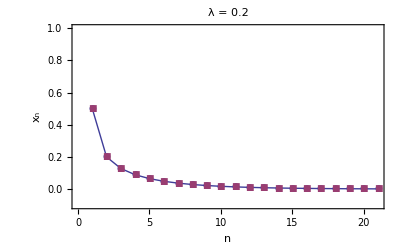

```mathematica
λ := 0.2
ListPlot[{NestList[f, 0.5, 20], NestList[f, 0.5, 20]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {-0.1, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 0.2"]
```

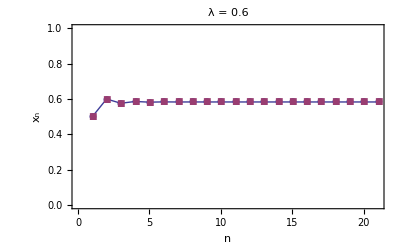

```mathematica
λ := 0.6
ListPlot[{NestList[f, 0.5, 20], NestList[f, 0.5, 20]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {0, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 0.6"]
```

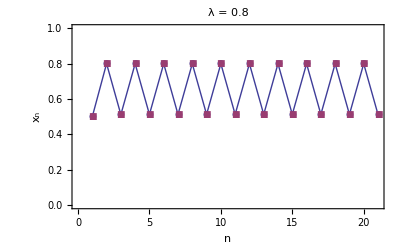

```mathematica
λ := 0.8
ListPlot[{NestList[f, 0.5, 20], NestList[f, 0.5, 20]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {0, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 0.8"]
```

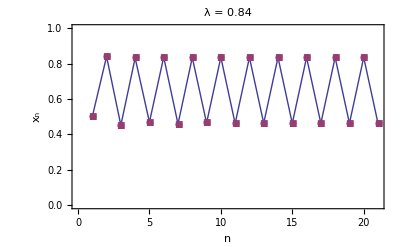

```mathematica
λ := 0.84
ListPlot[{NestList[f, 0.5, 20], NestList[f, 0.5, 20]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {0, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 0.84"]
```

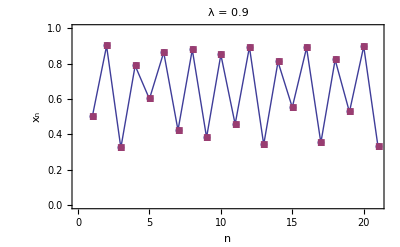

```mathematica
λ := 0.9
ListPlot[{NestList[f, 0.5, 20], NestList[f, 0.5, 20]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {0, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 0.9"]
```

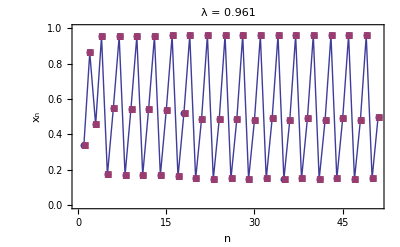

```mathematica
λ := 0.961
graph6 = ListPlot[{NestList[f, 0.34, 50], NestList[f, 0.34, 50]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {0, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 0.961"]
```

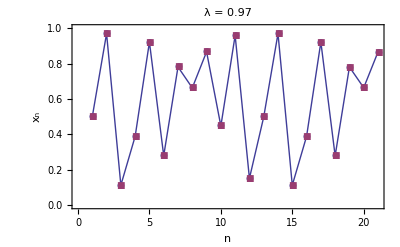

```mathematica
λ := 0.97
ListPlot[{NestList[f, 0.5, 20], NestList[f, 0.5, 20]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {0, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 0.97"]
```

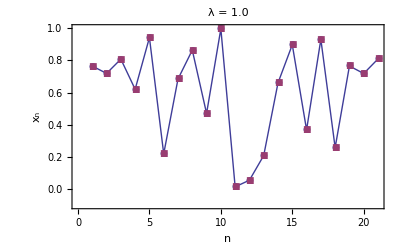

```mathematica
λ := 1.0
ListPlot[{NestList[f, 0.765, 20], NestList[f, 0.765, 20]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {-.1, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 1.0"]
```

λ = 0.2, 0.6: converges to fixed point
λ = 0.8, 0.84, 0.961: limit cycle
λ = 0.9, 0.97, 1.0: CHAOS!!!!!!!!!

Part b

```mathematica
lyapunov[lambda_, xinit_, n_, ninitialize_] := (λ = lambda; xlist = Drop[NestList[f, xinit, n], ninitialize+1]; Apply[Plus, Log[Abs[f'[xlist]]]]/Length[xlist])
```

λ = 0.2:

```mathematica
lyapunov[0.2, 0.5, 50000, 20]
```

-0.464708

λ = 0.6 :

```mathematica
lyapunov[0.6, 0.5, 50000, 20]
```

-0.748128

λ = 0.8 :

```mathematica
lyapunov[0.8, 0.5, 50000, 20]
```

-0.463043

λ = 0.84 :

```mathematica
lyapunov[0.84, 0.5, 50000, 20]
```

-0.175468

λ = 0.9 :

```mathematica
lyapunov[0.9, 0.5, 50000, 20]
```

0.182963

λ = 0.961 :

```mathematica
lyapunov[0.961, 0.5, 50000, 20]
```

-0.280351

λ = 0.97 :

```mathematica
lyapunov[0.97, 0.5, 50000, 20]
```

0.462067

λ = 1.0 :

```mathematica
lyapunov[1.0, 0.5, 50000, 20]
```

1.38629

If the lyapunov exponent is negative, it shows that the value of lambda iterates towards a single or multiple fixed points, whereas a positive lyapunov exponent yields represents a value of lambda which iterates towards chaos.

Part C :

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:= 4 λ x (1 - x);
f2[x_]:=f[f[x]];
f4[x_]:=f2[f2[x]];
f5[x_]:=f[f4[x]];
```

```mathematica
λ /. FindRoot[{f5[x] == x, f5'[x] == -1}, {x,0.93}, {λ,0.93}]
```

0.93528

```mathematica
λ=%
```

0.93528

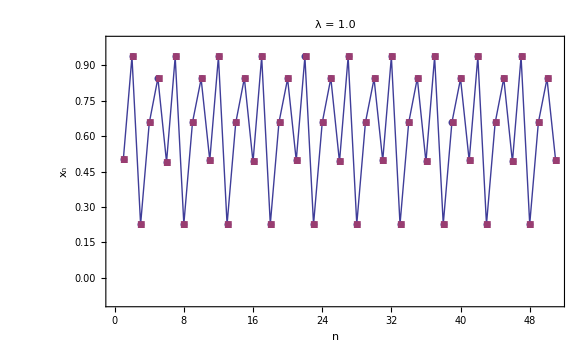

```mathematica
ListPlot[{NestList[f, 0.5, 50], NestList[f, 0.5, 50]}, Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n", Subscript["x","n"]}, PlotRange -> {-.1, 1}, PlotMarkers -> Automatic, RotateLabel -> False, PlotLabel -> "λ = 1.0"]
```

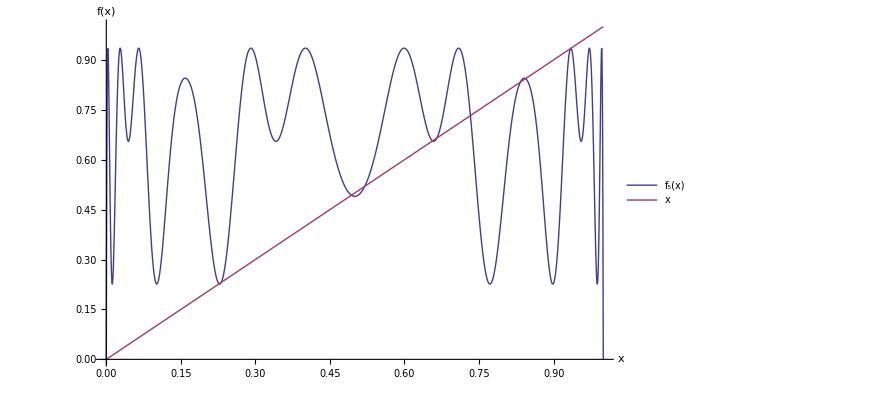

```mathematica
Plot[{f5[x],x},{x,0,1}, AxesLabel-> {"x", "f(x)"}, PlotLegends-> {"f_5(x)", "x"}]
```

By investigating the x vs. λ plot, I was able to find a rough estimate for λ and x to use for the "FindRoot" command.  By taking this value of lambda and iterating the function multiple times, I was able to visually represent the five fixed values of x to which the system oscillated. Finally, by comparing the fifth iteration of f(x) to just a straight line, I could identify the 5 stable points where the absolute value of the slope of the fifth iteration is less than one.

Part D :

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]:= 4 λ x (1 - x);
```

```mathematica
iterate [ m_,  n_]  := Drop [ NestList [f, 0.5, n], m]
```

```mathematica
drawpt[y_] := Point[{λ, y}]
```

```mathematica
graph[λmin_,λmax_, nλ_, mdrop_, n_] := Graphics [ {PointSize[0.005],Table [ Map[drawpt, iterate [mdrop,n ] ], {λ, λmin, λmax, (λmax-λmin)/nλ} ]}]
```

```mathematica
Show[graph[0.72,1,400,300,700],Axes->False,Frame->True,FrameLabel->{"λ","x"},PlotRange->{{0.9347, 0.9365},{0,1}},AspectRatio->1]
```

-Graphics-

When zooming in on the value of λ which corresponds to 5 fixed points, one can see that the period doubles to 10 fixed points at around λ = 0.9366. Note: The top and the bottom points are actual two distinct points which were obscured by the proximity to each other.

Part E :

```mathematica
f[x_]:= 4 λ x (1 - x);
f2[x_]:=f[f[x]]
f4[x_]:=f2[f2[x]]
f16[x_]:=f4[f4[x]]
```

λ_2:

```mathematica
lambda[2]=λ/. FindRoot[{f2[x] == x, f2'[x] == -1}, {x, 0.5}, {λ, 0.86}]
```

0.862372

λ_3:

```mathematica
lambda[3]=λ/. FindRoot[{f4[x]==x, f4'[x]==-1}, {x, 0.5}, {λ, 0.86}]
```

0.886023

λ_4:

```mathematica
lambda[4]=λ/. FindRoot[{f16[x] == x, f16'[x]==-1}, {x, 0.5}, {λ, 0.86}]
```

0.891102

```mathematica
lambda[0] := 0.25
lambda[1]:=0.75
```

```mathematica
δ[k_] := (lambda[k]-lambda[k-1])/(lambda[k+1]-lambda[k])
```

```mathematica
δ[1]
```

4.44949

```mathematica
δ[2]
```

4.75145

```mathematica
δ[3]
```

4.65625

Research shows that the Feigenbaum constant is about 4.669, which is the value the above deltas are oscillating towards.

### Question 7

Part a :

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]:=λ Sin[Pi x]
```

```mathematica
lyapunov[lambda_, xinit_, n_, ninitialize_] := (λ = lambda; xlist = Drop[NestList[f, xinit, n], ninitialize+1]; Apply[Plus, Log[Abs[f'[xlist]]]]/Length[xlist])
```

```mathematica
lyapunov[0.9, 0.5,50000, 20]
```

0.349115

The lyapunov exponent is positive, therefore the system is chaotic.

Part b :

```mathematica
f[x_]:= λ Sin[Pi x]
```

```mathematica
λ := N[9/10, 1000]
```

```mathematica
x0:= N[4/10, 1000]
```

```mathematica
N[NestList[f, x0, 5000], 1000][[5001]]
```

0.7955851371119273263202162429741831223365422769921380376888676446463754194303953557564236414408950409916024160011588298323581800232606390259976482533808870037739523385479486041306785401117712456881608003166286793755093127577232206610273568493440848426

```mathematica
Precision[%]
```

250.985